```mathematica
SetDirectory["/home/lindorfer/ReWiTech/Masterarbeit/Programs/Simplified_A/Data/"]
```

/home/lindorfer/ReWiTech/Masterarbeit/Daten

```mathematica
<<ModList.m
```

```mathematica
docks ={{0,4140,0},{4140,5160,9},{0,2640,1},{2640,4620,8},{0,2460,2},{2460,4440,7},{0,2400,3},{2400,4500,6},{0,2280,4},{2280,4500,5}}
```

{{0,4140,0},{4140,5160,9},{0,2640,1},{2640,4620,8},{0,2460,2},{2460,4440,7},{0,2400,3},{2400,4500,6},{0,2280,4},{2280,4500,5}}

```mathematica
?Take2
```

Take2[list_, a_, b_] Takes the Elements a & b of a sublist in list. Example: Take2[{{a,b,c,d,},{a,b,c,d}}, 1, 2] = {{a,b},{a,b}}.

```mathematica
times=Take2[docks,1,2]
```

{{0,4140},{4140,5160},{0,2640},{2640,4620},{0,2460},{2460,4440},{0,2400},{2400,4500},{0,2280},{2280,4500}}

```mathematica
Take[times,{2,3}]
```

{{4140,5160},{0,2640}}

```mathematica
Flatten[{Take[times,{1,2}],Take[times,{3,4}],Take[times,{5,6}]},0]
```

{{{0,4140},{4140,5160}},{{0,2640},{2640,4620}},{{0,2460},{2460,4440}}}

```mathematica
differences=Map[#[[2]]-#[[1]]&,times]
```

{4140,1020,2640,1980,2460,1980,2400,2100,2280,2220}

```mathematica
Take[differences,{1,2}]
```

{4140,1020}

```mathematica
Take[differences,All,{2}]
```

Take::take: Cannot take positions 2 through 2 in 4140.

Take[{4140,1020,2640,1980,2460,1980,2400,2100,2280,2220},All,{2}]

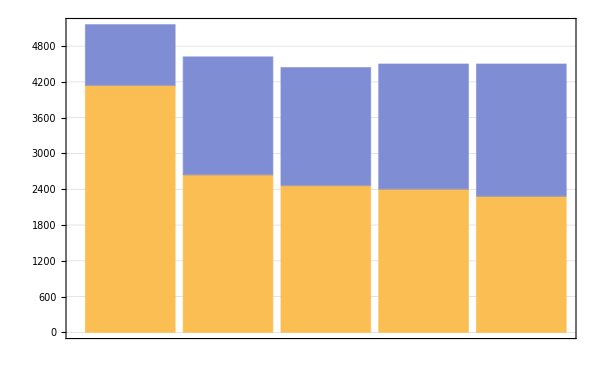

```mathematica
BarChart[{Take[differences,{1,2}],Take[differences,{3,4}],Take[differences,{5,6}],Take[differences,{7,8}],Take[differences,{9,10}]},
ChartLayout->"Stacked",
ImageSize->600,
Frame->True,
PlotTheme->"Detailed"]
```

```mathematica
d1={{0,1860,0},{1860,3720,5},{10000,11860,4},{15366,16806,9},{17822,19022,7},{21258,22278,0},{22568,23348,2},{26862,27642,3}};

d2={{0,1860,1},{1860,3720,6},{16680,17940,1},{18422,19502,3},{21590,22490,5},{27484,29224,8}};

d3={{0,1860,2},{1860,3720,7}};

d4={{0,1860,3},{1860,3720,8}};

d5={{0,1860,4},{1860,2880,9}};
```

```mathematica
d1=Take2[d1,1,2]
d2=Take2[d2,1,2]
d3=Take2[d3,1,2]
d4=Take2[d4,1,2]
d5=Take2[d5,1,2]
```

{{0,1860},{1860,3720},{10000,11860},{15366,16806},{17822,19022},{21258,22278},{22568,23348},{26862,27642}}

{{0,1860},{1860,3720},{16680,17940},{18422,19502},{21590,22490},{27484,29224}}

{{0,1860},{1860,3720}}

{{0,1860},{1860,3720}}

{{0,1860},{1860,2880}}

```mathematica
diffd1=Map[#[[2]]-#[[1]]&,d1];
diffd2=Map[#[[2]]-#[[1]]&,d2];
diffd3=Map[#[[2]]-#[[1]]&,d3];
diffd4=Map[#[[2]]-#[[1]]&,d4];
diffd5=Map[#[[2]]-#[[1]]&,d5];
```

```mathematica
getwaits[list_]:=Module[{i,waits={}},

For[i = 1, i <Length[list],i++,
AppendTo[waits,list[[i+1,1]]-list[[i,2]]];
];
Return[waits]
]
```

```mathematica
getbars[list1_,list2_]:=Module[{i,bars={}},

For[i=1, i< Length[list1],i++,

AppendTo[bars,list1[[i]]];
AppendTo[bars,list2[[i]]];
]
AppendTo[bars,list1[[Length[list1]]]];

Return[bars]
]
```

```mathematica
waitsd1=getwaits[d1]
waitsd2=getwaits[d2]
waitsd3=getwaits[d3]
waitsd4=getwaits[d4]
waitsd5=getwaits[d5]
```

{0,6280,3506,1016,2236,290,3514}

{0,12960,482,2088,4994}

{0}

{0}

{0}

```mathematica
barsd1=getbars[diffd1,waitsd1]
barsd2=getbars[diffd2,waitsd2]
barsd3=getbars[diffd3,waitsd3]
barsd4=getbars[diffd4,waitsd4]
barsd5=getbars[diffd5,waitsd5]
```

{1860,0,1860,6280,1860,3506,1440,1016,1200,2236,1020,290,780,3514,780}

{1860,0,1860,12960,1260,482,1080,2088,900,4994,1740}

{1860,0,1860}

{1860,0,1860}

{1860,0,1020}

```mathematica
color={};
For[i = 1, i< 15,i++,
AppendTo[color,Red];
AppendTo[color,White];
]
```

```mathematica
color
```

{RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1]}

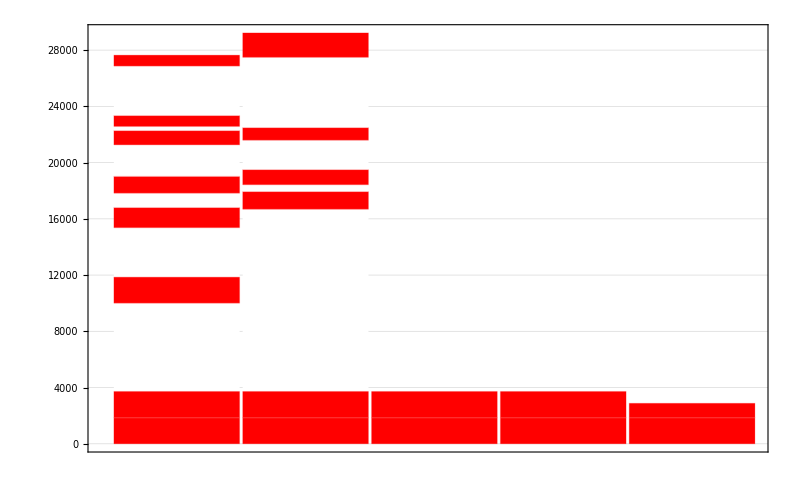

```mathematica
BarChart[{barsd1,barsd2,barsd3,barsd4,barsd5},
ChartLayout->"Stacked",
ImageSize->800,
Frame->True,
PlotTheme->"Detailed",
ChartStyle->color]
```